```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210519_time_windows_and_OR_model/module_reactions"];
```

```mathematica
Get["../../algoritm_packages/SingleNetworks-algorithm-package-2.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
stoichioforhomosapiens=Drop[Import["../../210324_disc_time_windows_and_OR_model/iAT_PLT_636_stoichiomat.csv",HeaderLines->1],None,{1}];
SparseArray@stoichioforhomosapiens
```

SparseArray[…]

```mathematica
stoichiometricmatrix=stoichioforhomosapiens;
metabolites=738;
fluxexchanges=1008;
steadystatevector=ConstantArray[{0,0},metabolites];
first[a_]:=First/@GatherBy[Ordering@a,a[[#]]&]//Sort;
```

community-1 nodes

```mathematica
community1nodes={4,6,9,11,12,15,17,19,22,24,28,30,32,35,37,42,44,45,50,56,57,58,59,61,65,66,70,74,76,78,79,81,86,88,90,98,101,102,103,105,107,112,113,114,118,124,129,130,132,133,135,139,142,144,145,149,152,154,155,160,162,164,169,170,173,178,179,183,185,188,190,192,194,198,201,204,205,209,210,212,213,216,217,218,219,221,222,223,231,232,234,240,241,248,249,257,258,264,270,279,284,285,291,296,299,300,301,304,317,318,319,320,322,329,331,334,342,343,344,346,350,359,362,368,370,375,378,379,380,381,382,384,385,386,387,388,395,403,405,408,409,410,413,414,415,418,419,420,428,431,433,434,436,440,450,455,458,459,462,465,466,467,469,470,471,478,479,481,482,489,491,518,520,526,527,531,532,533,539,547,551,553,556,564,566,571,572,576,578,581,595,597,601,606,612,615,622,625,626,630,632,636,637,640,644,646,648,649,650,657,658,668,669,670,671,674,676,679,680,682,683,684,685,687,690,693,699,705,707,715,720,721,725,729,732,735,738,739,741,743,745,760,764,783,784,786,800,801,803,807,809,811,813,815,816,818,819,820,821,823,824,827,833,839,845,846,850,858,863,864,865,866,868,871,875,881,886,893,898,899,906,910,914,916,919,921,922,924,926,929,930,933,938,944,946,956,962,966,969,997,1006};
```

```mathematica
subsetpositionfunction[reactions_]:=Module[{subsetsizechoice,subsetpositions},
subsetsizechoice=RandomInteger[{1,Length@reactions}];
subsetpositions=RandomSample[reactions,subsetsizechoice]]
```

```mathematica
subsetpositionsforsequences=Table[subsetpositionfunction[community1nodes],200];
boundaries=Import["../cases/boundaries_-5and5_105.mx"];
```

```mathematica
syntheticseqgenerator[stoichiometricmatrix_,steadystatevector_,boundaries_,fluxexchanges_,subsetpositions_]:=Module[{coefficients,objectivefunctions,solutionvectors},
coefficients=Table[RandomReal[{-1,1},Length@subsetpositions],300];
objectivefunctions=Table[ReplacePart[ConstantArray[0.,fluxexchanges],MapThread[#1->#2&,{subsetpositions,coefficients[[i]]}]],{i,300}];
solutionvectors=Chop[Table[LinearProgramming[-objectivefunctions[[i]],stoichiometricmatrix,steadystatevector,boundaries],{i,Length@objectivefunctions}],10^-5];{objectivefunctions,solutionvectors}]
```

```mathematica
AbsoluteTiming[resultset=Quiet@Table[syntheticseqgenerator[stoichiometricmatrix,steadystatevector,boundaries,fluxexchanges,i],{i,subsetpositionsforsequences}];]
```

{2975.86,Null}

```mathematica
Dimensions@resultset[[All,1]]
Dimensions@resultset[[All,2]]
```

{200,300,1008}

{200,300,1008}

```mathematica
(*Export["C:/Users/serha/NonDrive/modular_reactions/OR_model-solution_vectors/-1+1solutionvectors_fxdbounds_-5and5_105pcs.mx",resultset[[All,2]]]
Export["C:/Users/serha/NonDrive/modular_reactions/OR_model-objective_functions/-1+1objfunc_fxdbounds_-5and5_105pcs.mx",resultset[[All,1]]]*)
```

```mathematica
solutionvectors=resultset[[All,2]];
Length@first[(Flatten[solutionvectors,1])ᵀ]
Length@(Flatten[solutionvectors,1])[[first@Flatten[solutionvectors,1],All]]
```

1004

59404

```mathematica
objectivefunctions=resultset[[All,1]];
```

```mathematica
solutionvectors=Import["C:/Users/serha/NonDrive/modular_reactions/OR_model-solution_vectors/-1+1solutionvectors_fxdbounds_-5and5_105pcs.mx"];
```

```mathematica
SeedRandom@25;
deletionlist=Table[RandomInteger[1008,i],{i,Range[10,100,10]}];
```

```mathematica
solutionvectorsreactionsdeleted=Table[Partition[Delete[Transpose@Flatten[solutionvectors,1],Partition[deletionlist[[i]],1]]//Transpose,300],{i,10}];
```

```mathematica
objfunctionsreactionsdeleted=Table[Partition[Delete[Transpose@Flatten[objfunctions,1],Partition[deletionlist[[i]],1]]//Transpose,300],{i,10}];
```

```mathematica
AbsoluteTiming[featuredatalist=Table[MapThread[Dot,{objectivefunctions[[i]],solutionvectors[[i]]}],{i,200}];]
```

{1.04152,Null}

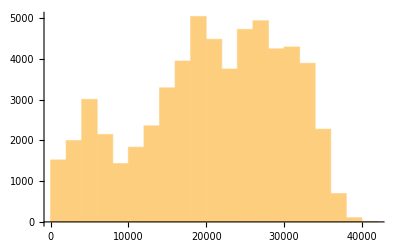

```mathematica
datafull=Join[Partition[Range@60000,1],Partition[Flatten@Table[ConstantArray[i,300],{i,200}],1],Partition[Flatten[featuredatalist,1],1],2];
Histogram@datafull[[All,3]]
```

```mathematica
AbsoluteTiming[widthdataFixedstep2=snetworkdatabinned[3,1000,datafull];]
```

{3.62584,Null}

```mathematica
graphsandnodenumbers12=snetworkgraph[widthdataFixedstep2[[1]],widthdataFixedstep2[[2]],2,7,400,Green];
graphsandnodenumbers12[[2]]
```

42

```mathematica
modularityvalues12=N@GraphAssortativity[graphsandnodenumbers12[[1]],FindGraphCommunities[graphsandnodenumbers12[[1]]],"Normalized"->False]
```

0.413171

```mathematica
singlerandomgraphsdegfxd12=Table[randomizinggraphdegfxd[i],{i,graphsandnodenumbers12[[All,1]]}];
singlerandomerdrenmodularityvalues12=Table[N@GraphAssortativity[singlerandomgraphsdegfxd12[[i]],FindGraphCommunities[singlerandomgraphsdegfxd12[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegfxd12}];
singlerandomgraphscomm12=Table[randomizinggraphmod[i],{i,graphsandnodenumbers12[[All,1]]}];
singlerandomcommmodularityvalues12=Table[N@GraphAssortativity[singlerandomgraphscomm12[[i]],FindGraphCommunities[singlerandomgraphscomm12[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm12}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity12=Table[zscorefunctionfortwonullmodels[i],{i,graphsandnodenumbers12[[All,1]]}];]
```

{79.5293,Null}

```mathematica
bucketnode12=graphsandnodenumbers12[[2]]
```

42

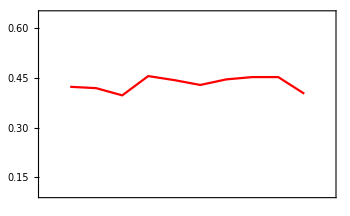
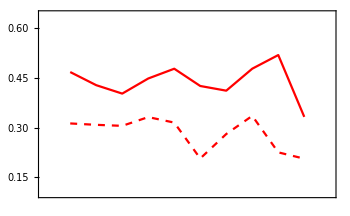
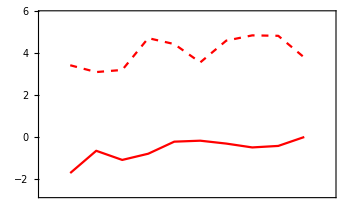

```mathematica
modularityvaluestimewinsmall=modularityvalues12;
randommodtimewinsmalldegreefxd=singlerandomerdrenmodularityvalues12;
randommodtimewinsmallcomm=singlerandomcommmodularityvalues12;
Zscoretimewinsmall=Zscoresmodularity12;
modularityplotrange={0.1,0.64};
(*MinMax[{modularityvalues1,singlerandomcommmodularityvalues1,singlerandomerdrenmodularityvalues1,modularityvalues12}]*)
padding=38;
win2=10;
Row[{ListLinePlot[Thread[{Range@win2,modularityvaluestimewinsmall}],Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0,win2+1},modularityplotrange}],
Row[{ListLinePlot[{Thread[{Range@win2,randommodtimewinsmalldegreefxd}],Thread[{Range@win2,randommodtimewinsmallcomm}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{0,win2+1},modularityplotrange}],
ListLinePlot[{Thread[{Range@win2,Zscoretimewinsmall[[All,1]]}],Thread[{Range@win2,Zscoretimewinsmall[[All,2]]}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{0,win2+1},MinMax[Flatten[Zscoretimewinsmall],1]}]}],LineLegend[{Dashed,Black},{"Degrees Fixed N.M.","Modularity N.M."},LegendMargins->0,LegendMarkerSize->{20,20}],Spacer@0.1}]
```

```mathematica
AbsoluteTiming[widthdataFixedbucket2=snetworkdatafxdbucket[3,bucketnode12,datafull];]
```

{1.52766,Null}

```mathematica
graphsandnodenumbers32=snetworkgraph[widthdataFixedbucket2[[1]],widthdataFixedbucket2[[2]],1.5,7,400,Green];
modularityvalues32=N@GraphAssortativity[graphsandnodenumbers32[[1]],FindGraphCommunities[graphsandnodenumbers32[[1]]],"Normalized"->False]
```

0.362753

```mathematica
singlerandomgraphsdegfxd32=Table[randomizinggraphdegfxd[i],{i,graphsandnodenumbers32[[All,1]]}];
singlerandomerdrenmodularityvalues32=Table[N@GraphAssortativity[singlerandomgraphsdegfxd32[[i]],FindGraphCommunities[singlerandomgraphsdegfxd32[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegfxd32}];
singlerandomgraphscomm32=Table[randomizinggraphmod[i],{i,graphsandnodenumbers32[[All,1]]}];
singlerandomcommmodularityvalues32=Table[N@GraphAssortativity[singlerandomgraphscomm32[[i]],FindGraphCommunities[singlerandomgraphscomm32[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm32}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity32=Table[zscorefunctionfortwonullmodels[i],{i,graphsandnodenumbers32[[All,1]]}];]
```

{68.9943,Null}

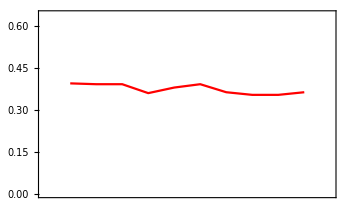
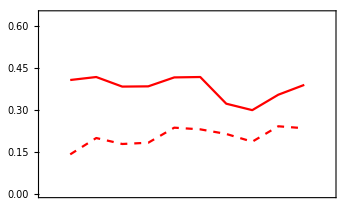
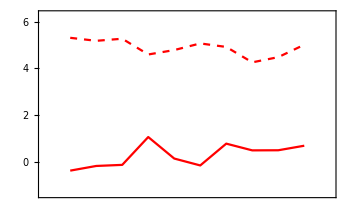

```mathematica
modularityvaluestimewinsmall=modularityvalues32;
randommodtimewinsmalldegreefxd=singlerandomerdrenmodularityvalues32;
randommodtimewinsmallcomm=singlerandomcommmodularityvalues32;
Zscoretimewinsmall=Zscoresmodularity32;
modularityplotrange={0,0.64};
(*MinMax[{modularityvalues1,singlerandomcommmodularityvalues1,singlerandomerdrenmodularityvalues1,modularityvalues12}]*)
padding=38;
win2=10;
Row[{ListLinePlot[Thread[{Range@win2,modularityvaluestimewinsmall}],Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0,win2+1},modularityplotrange}],
Row[{ListLinePlot[{Thread[{Range@win2,randommodtimewinsmalldegreefxd}],Thread[{Range@win2,randommodtimewinsmallcomm}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{0,win2+1},modularityplotrange}],
ListLinePlot[{Thread[{Range@win2,Zscoretimewinsmall[[All,1]]}],Thread[{Range@win2,Zscoretimewinsmall[[All,2]]}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{0,win2+1},MinMax[Flatten[Zscoretimewinsmall],1]}]}],LineLegend[{Dashed,Black},{"Degrees Fixed N.M.","Modularity N.M."},LegendMargins->0,LegendMarkerSize->{20,20}],Spacer@0.1}]
```

```mathematica
Export["plot_values/fxd_bounds/(-1,1)-modularityvalues-fss.mx",modularityvalues12]
Export["plot_values/fxd_bounds/(-1,1)-singrand-erd-modularityvalues-fss.mx",singlerandomerdrenmodularityvalues12]
Export["plot_values/fxd_bounds/(-1,1)-singrand-comm-modularityvalues-fss.mx",singlerandomcommmodularityvalues12]
Export["plot_values/fxd_bounds/(-1,1)-zscores-fss.mx",Zscoresmodularity12]
Export["plot_values/fxd_bounds/(-1,1)-modularityvalues-fbs.mx",modularityvalues32]
Export["plot_values/fxd_bounds/(-1,1)-singrand-erd-modularityvalues-fbs.mx",singlerandomerdrenmodularityvalues32]
Export["plot_values/fxd_bounds/(-1,1)-singrand-comm-modularityvalues-fbs.mx",singlerandomcommmodularityvalues32]
Export["plot_values/fxd_bounds/(-1,1)-zscores-fbs.mx",Zscoresmodularity32]
```

plot_values/fxd_bounds/(-1,1)-modularityvalues-fss.mx

plot_values/fxd_bounds/(-1,1)-singrand-erd-modularityvalues-fss.mx

plot_values/fxd_bounds/(-1,1)-singrand-comm-modularityvalues-fss.mx

plot_values/fxd_bounds/(-1,1)-zscores-fss.mx

plot_values/fxd_bounds/(-1,1)-modularityvalues-fbs.mx

plot_values/fxd_bounds/(-1,1)-singrand-erd-modularityvalues-fbs.mx

plot_values/fxd_bounds/(-1,1)-singrand-comm-modularityvalues-fbs.mx

plot_values/fxd_bounds/(-1,1)-zscores-fbs.mx